```mathematica
prodxs = 50;(*Higgs inclusive production cross section at 13 TeV*)
```

```mathematica
lum = 300/10^-3;(*300 fb^-1 luminostiy)
```

```mathematica
higgs = prodxs*lum; (*Number of higgs bosons produced*)
```

```mathematica
numevents[br_,eff_]:= higgs*br*eff;(*Number of events seen is the product of the number of higgs bosons produced multiplied by BR(h->ϕϕ) and the efficiency of detecting the ϕ->γγ decay products*)
```

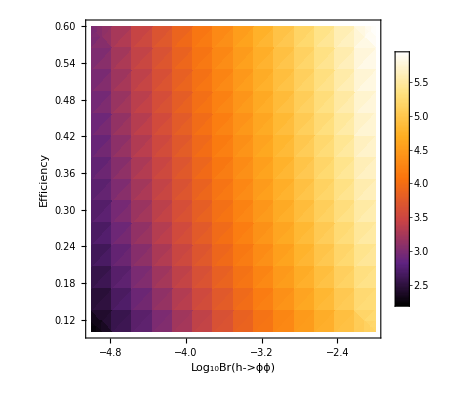

```mathematica
DensityPlot[Log10[numevents[10^x,y]],{x,-5.0,-2.0},{y,.1,.6},ColorFunction->"SunsetColors",PlotLegends->Automatic,FrameLabel->{"Log_10Br(h->ϕϕ)","Efficiency","Log_10Number of Events"},Ticks->{xticks,yticks,zticks}]
```

```mathematica
numevents[10^-4,.5]
```

7500.